# Dilatación de Stinespring

## Notas

La U_Stinespring está mal calculada porque no es una matriz unitaria

## Packages import and definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True](*desactiva check spelling*)
```

```mathematica
SFF[U_,dimU_Integer]:=Abs[Tr[U]]^2/dimU^2
```

## Parameters setup

```mathematica
L=8;(*number of spins*)
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.}}

```mathematica
(* Calcular eigenvalores y eigenvectores del Hamiltoniano del caometro *)
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(* Inicializar un estado aleatorio para los L-1 qubits del enotrno del caometro Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
```

## Calculations

```mathematica
(* Calcular superoperador *)
t=10.6;
superoperator=Superoperator[t, ψ0E, eigenvalsH, eigenvecsH, L]
```

{{0.61054+0. ⅈ,-0.0356611+0.0518909 ⅈ,-0.0356611-0.0518909 ⅈ,0.317605+0. ⅈ},{0.10424-0.197942 ⅈ,0.186087-0.118505 ⅈ,-0.00628259+0.0187999 ⅈ,-0.0716444-0.138168 ⅈ},{0.10424+0.197942 ⅈ,-0.00628259-0.0187999 ⅈ,0.186087+0.118505 ⅈ,-0.0716444+0.138168 ⅈ},{0.38946+0. ⅈ,0.0356611-0.0518909 ⅈ,0.0356611+0.0518909 ⅈ,0.682395+0. ⅈ}}

```mathematica
(* Calcular operadores de Kraus Subscript[K, i] del canal cuántico del caómetro *)
kraus=KrausOperatorsFromSuperoperator[Superoperator[t, ψ0E, eigenvalsH, eigenvecsH, L]]
```

{{{-0.362652+0.261198 ⅈ,0.0975957+0.111581 ⅈ},{-0.186296-0.0407488 ⅈ,-0.466395+0. ⅈ}},{{0.19679-0.170748 ⅈ,0.00742922+0.164356 ⅈ},{0.239172+0.19044 ⅈ,-0.319939+0. ⅈ}},{{-0.076312-0.0489371 ⅈ,-0.0739243-0.31103 ⅈ},{0.0519225+0.0949497 ⅈ,-0.0869849+0. ⅈ}},{{-0.16865+0.0314192 ⅈ,0.0481279+0.0723775 ⅈ},{0.102182+0.206737 ⅈ,0.117241+0. ⅈ}}}

```mathematica
(* Revisar que ∑_i Subscript[K, i]^†Subscript[K, i]=1/2 *)
MatrixForm@Chop[Total[ConjugateTranspose[#].#&/@kraus]]
```

(0.5 | 0
0 | 0.5)

```mathematica
A=2KroneckerProduct[#,#]&[FourierMatrix[2]]
```

{{1,1,1,1},{1,-1,1,-1},{1,1,-1,-1},{1,-1,-1,1}}

```mathematica
(* Definir una función para calcular la U de dilatación de Stinespring *)
U[ψ_,k_,l_,kraus_]:=Sum[A[[FromDigits[{k,l},2]+1,i]]KroneckerVectorProduct[kraus[[i]].VectorFromKetInComputationalBasis[{ψ}],VectorFromKetInComputationalBasis[IntegerDigits[i-1,2,2]]],{i,4}]
```

```mathematica
Ustinespring=√2 Transpose[Flatten[Table[U[ψ,i,k,kraus],{ψ,0,1},{i,0,1},{k,0,1}],2]]
```

{{1.,1.,1.,1.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,1.,1.,1.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

Aquí es dónde está mal

```mathematica
Ustinespring//UnitaryMatrixQ
```

False

```mathematica
MatrixPartialTrace[#.Dyad[VectorFromKetInComputationalBasis[{0,0,0}]].ConjugateTranspose[#]&[Ustinespring],2,{2,4}]//Tr
```

1.+0. ⅈ

```mathematica
superoperator.Flatten[Dyad[VectorFromKetInComputationalBasis[{0}]]]
```

{0.61054+0. ⅈ,0.10424-0.197942 ⅈ,0.10424+0.197942 ⅈ,0.38946+0. ⅈ}

```mathematica
Abs[Tr[Ustinespring]]^2/8^2
```

0.0192282

```mathematica
Abs[Tr[IdentityMatrix[8]]]^2/8.^2
```

1.

```mathematica
numberOftemporalPoints=500;
tValues=Flatten[Table[10.^(-3x/#+i),{i,3},{x,#/3,1,-1}]]&[numberOftemporalPoints]
```

{1.,1.01391,1.02802,1.04232,1.05682,1.07152,1.08643,1.10154,1.11686,1.1324,1.14815,1.16413,1.18032,1.19674,1.21339,1.23027,1.24738,1.26474,1.28233,1.30017,1.31826,1.3366,1.35519,1.37404,1.39316,1.41254,1.43219,1.45211,1.47231,1.49279,1.51356,1.53462,1.55597,1.57761,1.59956,1.62181,1.64437,1.66725,1.69044,1.71396,1.7378,1.76198,1.78649,1.81134,1.83654,1.86209,1.88799,1.91426,1.94089,1.96789,1.99526,2.02302,2.05116,2.0797,2.10863,2.13796,2.1677,2.19786,2.22844,2.25944,2.29087,2.32274,2.35505,2.38781,2.42103,2.45471,2.48886,2.52348,2.55859,2.59418,2.63027,2.66686,2.70396,2.74157,2.77971,2.81838,2.85759,2.89734,2.93765,2.97852,3.01995,3.06196,3.10456,3.14775,3.19154,3.23594,3.28095,3.3266,3.37287,3.41979,3.46737,3.5156,3.56451,3.6141,3.66438,3.71535,3.76704,3.81944,3.87258,3.92645,3.98107,4.03645,4.09261,4.14954,4.20727,4.2658,4.32514,4.38531,4.44631,4.50817,4.57088,4.63447,4.69894,4.76431,4.83059,4.89779,4.96592,5.03501,5.10505,5.17607,5.24807,5.32108,5.39511,5.47016,5.54626,5.62341,5.70164,5.78096,5.86138,5.94292,6.0256,6.10942,6.19441,6.28058,6.36796,6.45654,6.54636,6.63743,6.72977,6.82339,6.91831,7.01455,7.11214,7.21107,7.31139,7.4131,7.51623,7.62079,7.72681,7.8343,7.94328,8.05378,8.16582,8.27942,8.3946,8.51138,8.62979,8.74984,8.87156,8.99498,9.12011,9.24698,9.37562,9.50605,9.63829,9.77237,10.,10.1391,10.2802,10.4232,10.5682,10.7152,10.8643,11.0154,11.1686,11.324,11.4815,11.6413,11.8032,11.9674,12.1339,12.3027,12.4738,12.6474,12.8233,13.0017,13.1826,13.366,13.5519,13.7404,13.9316,14.1254,14.3219,14.5211,14.7231,14.9279,15.1356,15.3462,15.5597,15.7761,15.9956,16.2181,16.4437,16.6725,16.9044,17.1396,17.378,17.6198,17.8649,18.1134,18.3654,18.6209,18.8799,19.1426,19.4089,19.6789,19.9526,20.2302,20.5116,20.797,21.0863,21.3796,21.677,21.9786,22.2844,22.5944,22.9087,23.2274,23.5505,23.8781,24.2103,24.5471,24.8886,25.2348,25.5859,25.9418,26.3027,26.6686,27.0396,27.4157,27.7971,28.1838,28.5759,28.9734,29.3765,29.7852,30.1995,30.6196,31.0456,31.4775,31.9154,32.3594,32.8095,33.266,33.7287,34.1979,34.6737,35.156,35.6451,36.141,36.6438,37.1535,37.6704,38.1944,38.7258,39.2645,39.8107,40.3645,40.9261,41.4954,42.0727,42.658,43.2514,43.8531,44.4631,45.0817,45.7088,46.3447,46.9894,47.6431,48.3059,48.9779,49.6592,50.3501,51.0505,51.7607,52.4807,53.2108,53.9511,54.7016,55.4626,56.2341,57.0164,57.8096,58.6138,59.4292,60.256,61.0942,61.9441,62.8058,63.6796,64.5654,65.4636,66.3743,67.2977,68.2339,69.1831,70.1455,71.1214,72.1107,73.1139,74.131,75.1623,76.2079,77.2681,78.343,79.4328,80.5378,81.6582,82.7942,83.946,85.1138,86.2979,87.4984,88.7156,89.9498,91.2011,92.4698,93.7562,95.0605,96.3829,97.7237,100.,101.391,102.802,104.232,105.682,107.152,108.643,110.154,111.686,113.24,114.815,116.413,118.032,119.674,121.339,123.027,124.738,126.474,128.233,130.017,131.826,133.66,135.519,137.404,139.316,141.254,143.219,145.211,147.231,149.279,151.356,153.462,155.597,157.761,159.956,162.181,164.437,166.725,169.044,171.396,173.78,176.198,178.649,181.134,183.654,186.209,188.799,191.426,194.089,196.789,199.526,202.302,205.116,207.97,210.863,213.796,216.77,219.786,222.844,225.944,229.087,232.274,235.505,238.781,242.103,245.471,248.886,252.348,255.859,259.418,263.027,266.686,270.396,274.157,277.971,281.838,285.759,289.734,293.765,297.852,301.995,306.196,310.456,314.775,319.154,323.594,328.095,332.66,337.287,341.979,346.737,351.56,356.451,361.41,366.438,371.535,376.704,381.944,387.258,392.645,398.107,403.645,409.261,414.954,420.727,426.58,432.514,438.531,444.631,450.817,457.088,463.447,469.894,476.431,483.059,489.779,496.592,503.501,510.505,517.607,524.807,532.108,539.511,547.016,554.626,562.341,570.164,578.096,586.138,594.292,602.56,610.942,619.441,628.058,636.796,645.654,654.636,663.743,672.977,682.339,691.831,701.455,711.214,721.107,731.139,741.31,751.623,762.079,772.681,783.43,794.328,805.378,816.582,827.942,839.46,851.138,862.979,874.984,887.156,899.498,912.011,924.698,937.562,950.605,963.829,977.237}

```mathematica
Module[{superoperator,kraus,Ustinespring},
sffData=Table[
(* Calcular el superoperador ℰ̂ del canal cuántico del caómetro *)
superoperator=Chop@Superoperator[t, ψ0E, eigenvalsH, eigenvecsH, L];

(* Calcular operadores de Kraus Subscript[K, i] del canal cuántico del caómetro *)
kraus=KrausOperatorsFromSuperoperator[superoperator];

(* Calcular la unitaria de dilatación de Stinespring *)
Ustinespring=√2 Transpose[Flatten[Table[U[ψ,i,k,kraus],{ψ,0,1},{i,0,1},{k,0,1}],2]];

(* Calcular el SFF de la Ustinespring *)
SFF[Ustinespring,8]
,{t,tValues}];
]
```

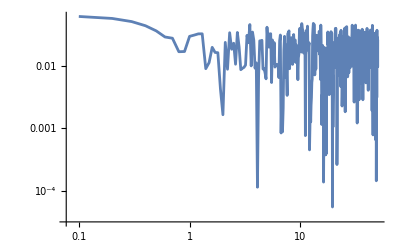

```mathematica
ListLogLogPlot[Transpose[{Range[0,50,0.1],sffData}],
Joined->True,
PlotRange->All]
```

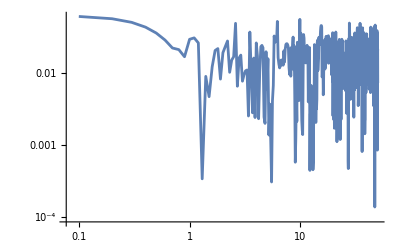

```mathematica
ListLogLogPlot[Transpose[{Range[0,50,0.1],sffData}],
Joined->True,
PlotRange->All]
```

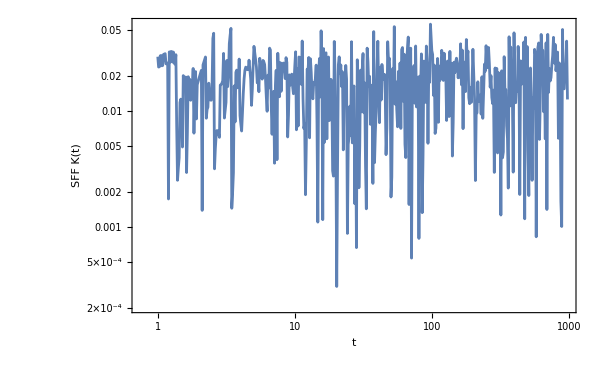

```mathematica
ListLogLogPlot[Transpose[{tValues,sffData}],
Joined->True,
PlotRange->All,
Frame->True,FrameLabel->{TraditionalForm[HoldForm[t]],"SFF K(t)"},
FrameStyle->Directive[Black,FontSize->20,FontFamily->"Arial"],
ImageSize->600
]
```